# NGW 30-DOF 行星轮系 · Mathematica 独立验证

## 1 · 固有频率谱（广义特征值 K φ = ω.b2 M φ）

模态数 = 29     最低两阶 = 1544.83320431 / 1544.83320431 Hz

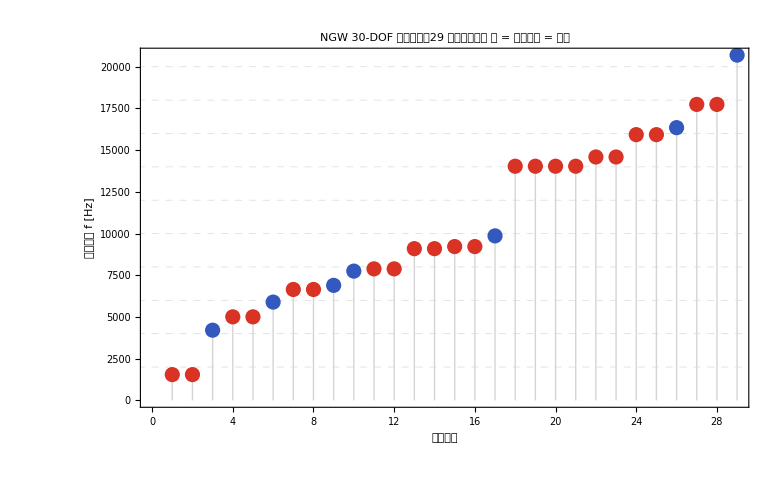

```mathematica
ex = "D:/AAAAAAAAAAAAAAAAAAAMyFile/Doctor/Research/ngw_final/results_doc/ngw_export";
readM[f_] := Module[{d = Import[FileNameJoin[{ex, f}], "Table", "FieldSeparators" -> ","]},
   If[VectorQ[d], List /@ d, d]];
Ktot = readM["K_struct.csv"] + readM["K_mesh_avg.csv"];
Mmat = readM["M.csv"];
lam = Chop[Eigenvalues[{Ktot, Mmat}]];
fMM = Sort@Select[Sqrt@Clip[Re[lam], {0., Infinity}], # > 1. &]/(2. Pi);
keys = Round[1000. fMM];
cnt = Counts[keys];
cols = Lookup[cnt, keys];
styled = MapThread[
   Style[#1, Directive[PointSize[0.014],
      If[#2 > 1, RGBColor[0.85, 0.20, 0.15], RGBColor[0.20, 0.35, 0.75]]]] &,
   {fMM, cols}];
Print[Row[{"模态数 = ", Length[fMM], "     最低两阶 = ",
    NumberForm[fMM[[1]], 12], " / ", NumberForm[fMM[[2]], 12], " Hz"}]];
ListPlot[styled,
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.30], GrayLevel[0.45]],
  Frame -> True,
  FrameLabel -> {{"固有频率  f  [Hz]", ""}, {"模态序号", ""}},
  PlotLabel -> "NGW 30-DOF 固有频率（29 阶非零模态）\n红 = 重根，蓝 = 单根",
  GridLines -> {None, Table[k 2000, {k, 1, 11}]},
  GridLinesStyle -> Directive[LightGray, Dashed],
  BaseStyle -> {FontSize -> 12},
  ImageSize -> 780]
```

## 2 · 啮合力时程（实线 = 外啮合 F_sp，虚线 = 内啮合 F_rp）

采样点 = 3001    dt = 0.0001 s    t_end = 0.3 s

末时刻 F_sp = {28.359, 30.3892, 29.9162} N

末时刻 F_rp = {-28.3563, -30.3817, -29.9138} N

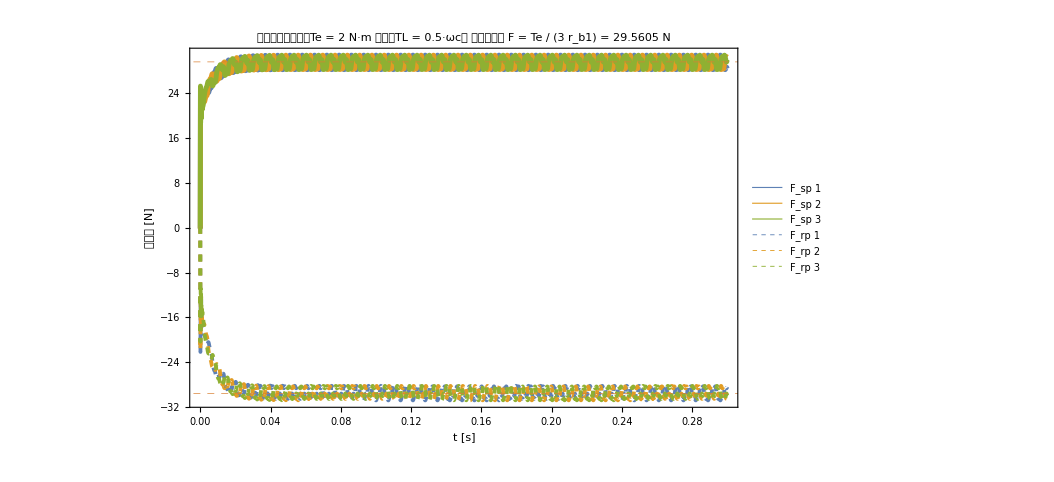

```mathematica
t = Flatten[readM["ref_t.csv"]];
Fm = readM["ref_Fmesh.csv"];
spCols = {1, 3, 5}; rpCols = {2, 4, 6};
Print[Row[{"采样点 = ", Length[t], "    dt = ", t[[2]] - t[[1]], " s    t_end = ", t[[-1]], " s"}]];
Print[Row[{"末时刻 F_sp = ", NumberForm[Fm[[-1, spCols]], 6], " N"}]];
Print[Row[{"末时刻 F_rp = ", NumberForm[Fm[[-1, rpCols]], 6], " N"}]];
ListLinePlot[
  Join[Table[Transpose[{t, Fm[[All, i]]}], {i, spCols}],
       Table[Transpose[{t, Fm[[All, i]]}], {i, rpCols}]],
  PlotStyle -> Join[
    Table[Directive[Thickness[0.0045], ColorData[97][k]], {k, 1, 3}],
    Table[Directive[Thickness[0.0035], Dashed, ColorData[97][k]], {k, 1, 3}]],
  PlotLegends -> LineLegend[{"F_sp 1", "F_sp 2", "F_sp 3", "F_rp 1", "F_rp 2", "F_rp 3"},
    LegendLayout -> {"Row", 3}],
  Frame -> True,
  FrameLabel -> {{"啮合力  [N]", ""}, {"t  [s]", ""}},
  PlotLabel -> "三路啮合力时程（Te = 2 N·m 常值，TL = 0.5·ωc）\n理论静态值 F = Te / (3 r_b1) = 29.5605 N",
  GridLines -> {None, {-29.5605, 29.5605}},
  GridLinesStyle -> Directive[RGBColor[0.85, 0.5, 0.2], Dashed],
  BaseStyle -> {FontSize -> 12},
  ImageSize -> 780]
```

## 3 · 频谱：啮频及其谐波、边频

采样率 = 10000. Hz   频率分辨率 = 3.33222 Hz

检出主峰 [Hz] = {2.08264, 5.83139, 9.16361, 12.9124, 16.2446, 142.869}

理论: f_mesh = 142.857, 2f = 285.714, 3f = 428.571, 4f = 571.429, 5f = 714.286

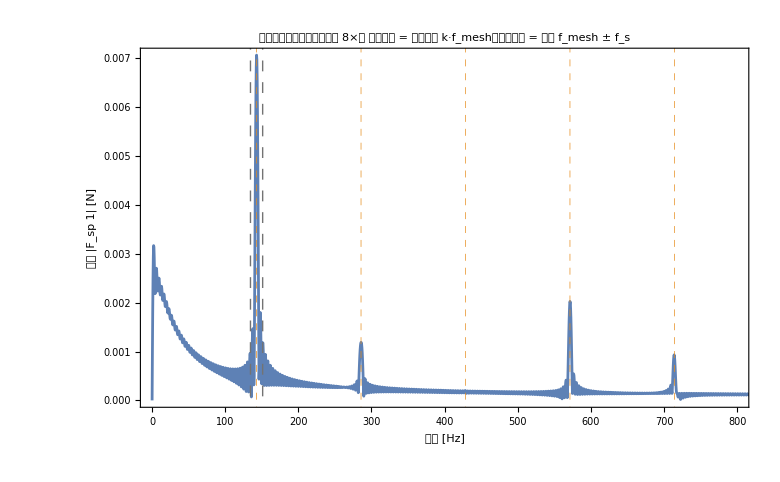

```mathematica
dt = t[[2]] - t[[1]];
fsr = 1./dt;
x = Fm[[All, 1]] - Mean[Fm[[All, 1]]];
nx = Length[x];
nz = 8 nx;
X = Abs[Fourier[PadRight[x, nz]]] 2./nx;
nf = Floor[nz/2];
fr = Table[(k - 1.)/(nz dt), {k, 1, nf}];
amp = X[[1 ;; nf]];
locmax = Select[Range[2, nf - 1], amp[[#]] > amp[[# - 1]] && amp[[#]] > amp[[# + 1]] &];
top = TakeLargestBy[locmax, amp[[#]] &, 6];
pk = SortBy[Table[{fr[[k]], amp[[k]]}, {k, top}], First];
Print[Row[{"采样率 = ", fsr, " Hz   频率分辨率 = ", 1./(nx dt), " Hz"}]];
Print[Row[{"检出主峰 [Hz] = ", NumberForm[pk[[All, 1]], 6]}]];
Print[Row[{"理论: f_mesh = 142.857, 2f = 285.714, 3f = 428.571, 4f = 571.429, 5f = 714.286"}]];
fmesh = 142.85714285714286; fs1 = 8.333333333333334;
ListLinePlot[Transpose[{fr, amp}],
  PlotRange -> {{0, 800}, All},
  Frame -> True,
  FrameLabel -> {{"幅值   |F_sp 1|  [N]", ""}, {"频率  [Hz]", ""}},
  PlotLabel -> "外啮合啮合力频谱（零填充 8×）\n橙色虚线 = 啮频谐波 k·f_mesh；灰色点线 = 边频 f_mesh ± f_s",
  GridLines -> {
    Table[k fmesh, {k, 1, 5}],
    None},
  GridLinesStyle -> Directive[RGBColor[0.9, 0.55, 0.1], Dashed],
  Epilog -> {
    GrayLevel[0.45], Dashing[{0.01, 0.01}],
    InfiniteLine[{{fmesh - fs1, 0}, {fmesh - fs1, 1}}],
    InfiniteLine[{{fmesh + fs1, 0}, {fmesh + fs1, 1}}]},
  BaseStyle -> {FontSize -> 12},
  ImageSize -> 780]
```